```mathematica
SetDirectory["G:\\My Drive\\Projects\\FourierDisplay\\Software"];
LoadPack:=Get["G:\\My Drive\\Projects\\FourierDisplay\\Software\\FourierPack.wl"];
LoadPack;
```

Spinner::shdw: Symbol Spinner appears in multiple contexts {FourierPack`,Global`}; definitions in context FourierPack` may shadow or be shadowed by other definitions.

```mathematica
hexToRGB[hex_]:=RGBColor@@(N[FromDigits[StringJoin[#],12]/255]&/@Partition[Characters[hex],2]);
themeColors = hexToRGB/@{"023859","056C83","DDCCC2","CA431E","D86334"}
```

{RGBColor[0.00784313725490196, 0.17254901960784313, 0.27058823529411763],RGBColor[0.0196078431372549, 0.32941176470588235, 0.38823529411764707],RGBColor[0.6627450980392157, 0.611764705882353, 0.5725490196078431],RGBColor[0.6039215686274509, 0.2, 0.10196078431372549],RGBColor[0.6431372549019608, 0.29411764705882354, 0.1568627450980392]}

## Spinner Graphic

```mathematica
Manipulate[Graphics[{themeColors[[1]],Arrow[{{0,0},length*{Cos@θ,Sin@θ}}]}],{length,0,5},{θ,0,2π}]
```

Part::partd: Part specification themeColors⟦1⟧ is longer than depth of object.

```mathematica
Manipulate[With[{func=Function[t,Exp[2π I t]]},
Module[{radius = Abs@func[0], form =TraditionalForm[func["t"]]},
Column[{
Graphics[GraphicsComplex[{{0.,0.},ReIm@func[0],ReIm@func[t]},
{Thickness[.005],
{themeColors[[3]],Dashed,Line[{1,2}]},
{themeColors[[1]],Arrow[{1,3}]},
{themeColors[[2]],Opacity[.5],Circle[radius,1]}
}],
PlotRange->radius,PlotRangePadding->Scaled[.05],Frame->False],
Style[form,"Subtitle", themeColors[[5]]]},Center]]],{t,0,1}]
```

Part::partd: Part specification themeColors⟦3⟧ is longer than depth of object.

Part::partd: Part specification themeColors⟦1⟧ is longer than depth of object.

Part::partd: Part specification themeColors⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification themeColors⟦3⟧ is longer than depth of object.

Part::partd: Part specification themeColors⟦1⟧ is longer than depth of object.

Part::partd: Part specification themeColors⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification themeColors⟦3⟧ is longer than depth of object.

Part::partd: Part specification themeColors⟦1⟧ is longer than depth of object.

Part::partd: Part specification themeColors⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification themeColors⟦3⟧ is longer than depth of object.

Part::partd: Part specification themeColors⟦1⟧ is longer than depth of object.

Part::partd: Part specification themeColors⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*With[{func=Function[t,Exp[2π I t]]},
DynamicModule[{radius = Abs@func[0], form =TraditionalForm[func["t"]] },
Dynamic[t0= Clock[{0,Infinity}];
Column[{
Graphics[GraphicsComplex[{{0.,0.},ReIm@func[0],ReIm@func[t0]},
{Thickness[.005],
{themeColors[[3]],Dashed,Line[{1,2}]},
{themeColors[[1]],Arrow[{1,3}]},
{themeColors[[2]],Opacity[.5],Circle[radius,1]}
}],
PlotRange->radius,PlotRangePadding->Scaled[.05],Frame->False],
Style[form,"Subtitle", themeColors[[5]]]},Center]]]]*)
```

```mathematica
(*With[{func=Function[t,Exp[2π I t]]},
DynamicModule[{radius = Abs@func[0], form =TraditionalForm[func["t"]], t0=0 },
Deploy@Column[{
Animator[Dynamic[t0],{0,1},AnimationRate->1,Enabled->False, AppearanceElements->None],
Graphics[Dynamic@GraphicsComplex[{{0.,0.},ReIm@func[0],ReIm@func[t0]},
{Thickness[.005],
{themeColors[[3]],Dashed,Line[{1,2}]},
{themeColors[[1]],Arrow[{1,3}]},
{themeColors[[2]],Opacity[.5],Circle[radius,1]}
}],
PlotRange->radius,PlotRangePadding->Scaled[.05],Frame->False],
Style[form,"Subtitle", themeColors[[5]]]
},Center]]]
```

```mathematica
(*Spinner[function_,{t_Symbol,a_,b_}]:=
With[{func=Function[i,(function/.t->i)]},
DynamicModule[{radius = Abs@func[0], form =TraditionalForm[func["t"]], t0=0 },
Deploy@Column[{
Animator[Dynamic[t0],{a,b},AnimationRate->1,Enabled->False, AppearanceElements->None],
Graphics[Dynamic@GraphicsComplex[{{0.,0.},ReIm@func[0],ReIm@func[t0]},
{Thickness[.005],
{themeColors[[3]],Dashed,Line[{1,2}]},
{themeColors[[1]],Arrow[{1,3}]},
{themeColors[[2]],Opacity[.5],Circle[radius,1]}
}],
PlotRange->radius,PlotRangePadding->Scaled[.05],Frame->False],
Style[form,"Subtitle", themeColors[[5]]]
},Center]]]*)
```

```mathematica
(*Spinner[Exp[2 I π t],{t,0,1}]
```

```mathematica
(*Options[Spinner] = {"AngleViewer"->False};
Spinner[function_,t_,$t_, OptionsPattern[]]:=
With[{func=Function[i,(function/.t->i)]},
With[{radius = Abs@func[0], form =TraditionalForm[func["t"]],points = {{0.,0.},ReIm@func[0],ReIm@func[$t]}},
Deploy@Column[{
Show[{Graphics[GraphicsComplex[points,
{Thickness[.005],
{themeColors[[3]],Dashed,Line[{1,2}]},
{themeColors[[1]],Arrow[{1,3}]},
{themeColors[[2]],Opacity[.5],Circle[radius,1]}
}],PlotRange->radius,PlotRangePadding->Scaled[.05],Frame->False],
Evaluate@If[OptionValue["AngleViewer"]===True,{With[{angleRad = .5},{ParametricPlot[angleRad*ReIm@func[t],{t,0,$t},PlotStyle->themeColors[[3]],Axes->False]/.Line[x_,___]:> {Arrowheads[{-Medium,Medium}],Dashed,Arrow[x]},
Graphics[Text[Style[StringForm["θ=``°",PlanarAngle[points]/Degree], "Bold","Medium", themeColors[[3]]],1.1*angleRad*ReIm@func[($t-0)/5], {-1,0}]]}]},{}]}, "PlotRange"->All],
Style[form,"Subtitle", themeColors[[5]]]
},Center]]]*)
```

```mathematica
Options[Spinner] = {"FunctionViewer"->False,"AngleViewer"->False, "StatViewer"->False, "MaxRadius"->None};
Spinner[{coef_, ω_},$t_,OptionsPattern[]]:=
With[{func=Function[t,coef*Exp[I ω t]]},
Module[{radius = Abs@coef, form =TraditionalForm[NumberForm[coef,{Infinity,1}]*Exp[NumberForm[ω,{∞,1}]*I *"t"]],angle = (ω $t+Arg[coef])/Degree, angle0 = Arg[coef]/Degree, scalePadding },
scalePadding = If[OptionValue["MaxRadius"]===None,Scaled[.05],OptionValue["MaxRadius"]-radius];
Deploy@Column[{
Show[{
Graphics[GraphicsComplex[{{0.,0.},ReIm@coef,ReIm@func[$t]},
{Thickness[.005],
{themeColors[[3]],Dashed,Line[{1,2}]},
{themeColors[[1]],Arrow[{1,3}]},
{themeColors[[2]],Opacity[.5],Circle[1,radius]}
}],PlotRangePadding->scalePadding,Frame->False],
If[OptionValue["AngleViewer"]===True,With[{angleRad = .5},
{If[angle-angle0>0.1,{ParametricPlot[angleRad*ReIm@func[t],{t,0,$t},PlotStyle->themeColors[[3]],Axes->False]/.Line[x_,___]:> {Arrowheads[{-Small,Small}],Dashed,Arrow[x]}},{}],
Graphics[Text[Style["θ", themeColors[[3]],Bold],1.2*angleRad*ReIm@func[($t-0)/2], {0,0}]]}],
{}]}, "PlotRange"->All]}//
If[OptionValue["AngleViewer"]===True,Insert[#,Style[StringForm["θ=``°",NumberForm[angle, {Infinity,1}]], "Bold","Medium", themeColors[[5]]],-1],#]&//
If[OptionValue["FunctionViewer"]===True,
Insert[#,Style[form,"Medium", themeColors[[5]]],-1],#]&//
If[OptionValue["StatViewer"]===True,
Insert[#,Column[Style[#,"Bold","Text",themeColors[[5]]]&/@{StringForm["L = ``",NumberForm[radius,{Infinity,1}]],StringForm["θ_0 = ``°",NumberForm[angle0,{Infinity,1}]],StringForm["ω = ``deg/s",NumberForm[(ω/N@Degree),{Infinity,1}]]},Center],-1],#]&
,Center]]]
```

```mathematica
ReIm@1.1
```

{1.1,0}

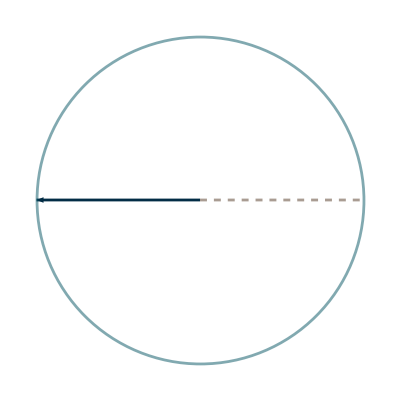
-Graphics-
L = 2.5
θ_0 = 0°
ω = 360.0deg/s

```mathematica
Spinner[{2.5,2π},.5, "StatViewer"->True, "MaxRadius"->10]
```

```mathematica
Transpose[{Range[5],Range[5]}]
```

{{1,1},{2,2},{3,3},{4,4},{5,5}}

```mathematica
With[{spinners ={{.1+1I,1},{10,5}, {5,2}}}, Manipulate[Row@(Spinner[#,n, "AngleViewer"->True, "MaxRadius"->Max@Abs@spinners[[All,1]]]&/@spinners),{n,0,1}]]
```

ParametricPlot::plld: Endpoints for t in {t,0,0} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{,{{ParametricPlot[0.5 ReIm[(«2»&)[«1»]],{t,0,0},PlotStyle→themeColors⟦3⟧,Axes→False],}}},PlotRange→All].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::plld: Endpoints for t in {t,0,0} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{,{{ParametricPlot[0.5 ReIm[(«2»&)[«1»]],{t,0,0},PlotStyle→themeColors⟦3⟧,Axes→False]},}},PlotRange→All].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

### Another option for Degree Indicator

```mathematica
Manipulate[
With[{func = Function[t,ReIm@Exp[2 I π t]], angle = Function[{θ1,θ2},2 π (θ2-θ1)]},
Show[{ParametricPlot[.5*func[t],{t,θ1,θ2},PlotStyle->themeColors[[3]],Axes->False]/.Line[x_,___]:> {Arrowheads[{-Medium,Medium}],Dashed,Arrow[x]},
Graphics[Text[Style[StringForm["θ=``°",angle[θ1,θ2]/Degree], "Bold","Large", themeColors[[3]]],.55*ReIm@Exp[2I π (θ1+θ2)/5], {-1,0}]]
}]],{θ1,0,1},{θ2,0,1}]
```

Part::partd: Part specification themeColors⟦3⟧ is longer than depth of object.

## Test Package Function